# Progetto di Matematica computazionale

```mathematica
Quit[];
```

```mathematica
NotebookDir = NotebookDirectory[];
SetDirectory[NotebookDir];
Get["ENC.wls"];
```

```mathematica
(*Trasforma una stringa nella lista di codici ascii corrispondenti*)
inputString=InputString["Inserisci la tua stringa:"];
MaxErrors = 10; (*Creare slider*)
StrEncode[inputString, MaxErrors]
```

```mathematica
asciiList =ToCharacterCode[inputString];
```

ciao

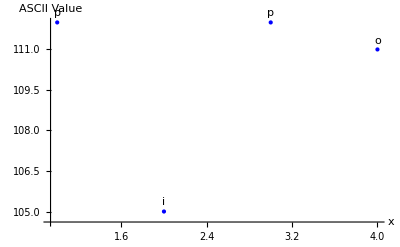

```mathematica
(*Plot original points function*)
points = Transpose[{Range[Length[asciiList]],asciiList}];
charList=Characters[inputString];
labeledPoints=Transpose[{points,charList}];
labeledPointsList=Labeled[#[[1]],#[[2]],Above]&/@labeledPoints;
ListPlot[labeledPointsList,PlotStyle->{PointSize[Medium],Blue},AxesLabel->{"x","ASCII Value"}]
```

155-(205 x)/3+29 x^2-(11 x^3)/3

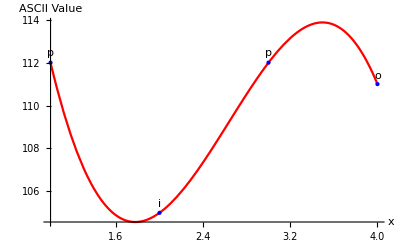

```mathematica
(*Plot polynomial*)
polynomial = Expand[InterpolatingPolynomial[points, x]]
Show[Plot[polynomial,{x,1,Length[asciiList]},PlotStyle->Red,AxesLabel->{"x","ASCII Value"}],ListPlot[labeledPointsList,PlotStyle->{PointSize[Medium], Blue}]]
```

```mathematica
(*Error Retrival points*)
maxErrors = 10;
expandedPoints=Table[{i,polynomial/. x->i},{i,Length[points]+maxErrors}];
asciiListExpanded=Round[Last/@expandedPoints];
stringExpanded = FromCharacterCode[asciiListExpanded]
charListExpanded=FromCharacterCode/@asciiListExpanded;
labeledPointsExpanded=Transpose[{expandedPoints,charListExpanded}];
labeledPointsExpandedList=Labeled[#[[1]],#[[2]],Above]&/@labeledPointsExpanded;
```

FromCharacterCode::notunicode: A character code, which should be a non-negative integer less than 1114112, is expected at position 6 in {112,105,112,111,80,-3,-160,-413,-784,-1295,«4»}.

FromCharacterCode[{112,105,112,111,80,-3,-160,-413,-784,-1295,-1968,-2825,-3888,-5179}]

FromCharacterCode::intnm: Non-negative machine-sized integer expected at position 1 in FromCharacterCode[-3].

FromCharacterCode::intnm: Non-negative machine-sized integer expected at position 1 in FromCharacterCode[-160].

FromCharacterCode::intnm: Non-negative machine-sized integer expected at position 1 in FromCharacterCode[-413].

General::stop: Further output of FromCharacterCode::intnm will be suppressed during this calculation.

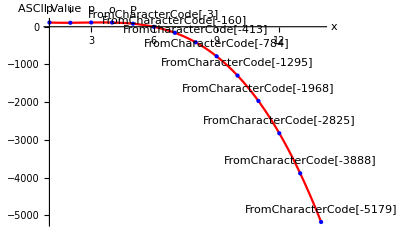

```mathematica
(*Plot polynomial with retriaval error points*)
Show[Plot[polynomial,{x,1,Length[expandedPoints]},PlotStyle->Red,AxesLabel->{"x","ASCII Value"}],ListPlot[labeledPointsExpandedList,PlotStyle->{PointSize[Medium],Blue}]]
```

```mathematica
(* String dirter*)
nErrors = RandomInteger[{1,maxErrors}]
errorsPos= RandomSample[Range[StringLength[stringExpanded]],nErrors]

myStringAsList=Characters[stringExpanded];
myStringAsList=Delete[myStringAsList,List/@errorsPos];
corruptedString=StringJoin[myStringAsList]

strLen = StringLength[stringExpanded]
```

8

StringLength::string: String expected at position 1 in StringLength[FromCharacterCode[{112,105,112,111,80,-3,-160,-413,-784,-1295,«4»}]].

Range::range: Range specification in Range[StringLength[FromCharacterCode[{112,105,112,111,80,-3,-160,-413,-784,-1295,«4»}]]] does not have appropriate bounds.

RandomSample::lrwl: The set of items to sample from, Range[StringLength[FromCharacterCode[{112,105,112,111,80,-3,-160,-413,-784,-1295,«4»}]]], should be a non-empty list or a rule weights -> choices.

RandomSample[Range[StringLength[FromCharacterCode[{112,105,112,111,80,-3,-160,-413,-784,-1295,-1968,-2825,-3888,-5179}]]],8]

RandomSample::intnm: Non-negative machine-sized integer expected at position 2 in RandomSample[{Range[StringLength[FromCharacterCode[{112,105,112,111,80,-3,-160,-413,-784,-1295,«4»}]]]},{8}].

Delete::pkspec: The expression RandomSample[{Range[StringLength[FromCharacterCode[{112,105,112,111,80,-3,-160,-413,-784,-1295,«4»}]]]},{8}] cannot be used as a part specification. Use Key[RandomSample[{Range[StringLength[FromCharacterCode[{112,105,112,111,80,-3,-160,-413,-784,-1295,«4»}]]]},{8}]] instead.

StringJoin::string: String expected at position 1 in StringJoin[Delete[Characters[FromCharacterCode[{112,105,112,111,80,-3,-160,-413,-784,-1295,«4»}]],RandomSample[{Range[StringLength[FromCharacterCode[{«14»}]]]},{8}]]].

StringJoin[Delete[Characters[FromCharacterCode[{112,105,112,111,80,-3,-160,-413,-784,-1295,-1968,-2825,-3888,-5179}]],RandomSample[{Range[StringLength[FromCharacterCode[{112,105,112,111,80,-3,-160,-413,-784,-1295,-1968,-2825,-3888,-5179}]]]},{8}]]]

StringLength::string: String expected at position 1 in StringLength[FromCharacterCode[{112,105,112,111,80,-3,-160,-413,-784,-1295,«4»}]].

StringLength[FromCharacterCode[{112,105,112,111,80,-3,-160,-413,-784,-1295,-1968,-2825,-3888,-5179}]]

## ...

```mathematica
(*msg_received =  [corruptedString, errorsPos, strLen, maxErrors];*)
```

```mathematica
asciiList =ToCharacterCode[corruptedString]
charList = Characters[corruptedString];
charsPos=Complement[Range[strLen], errorsPos]
points = Transpose[{charsPos,asciiList}]
labeledPoints=Transpose[{points,charList}]
labeledPointsList=Labeled[#[[1]],#[[2]],Above]&/@labeledPoints;
```

ToCharacterCode::strse: String or list of strings expected at position 1 in ToCharacterCode[StringJoin[Delete[Characters[FromCharacterCode[{112,105,112,111,80,-3,-160,-413,-784,-1295,«4»}]],RandomSample[{Range[StringLength[FromCharacterCode[«1»]]]},{8}]]]].

ToCharacterCode[StringJoin[Delete[Characters[FromCharacterCode[{112,105,112,111,80,-3,-160,-413,-784,-1295,-1968,-2825,-3888,-5179}]],RandomSample[{Range[StringLength[FromCharacterCode[{112,105,112,111,80,-3,-160,-413,-784,-1295,-1968,-2825,-3888,-5179}]]]},{8}]]]]

Range::range: Range specification in Range[StringLength[FromCharacterCode[{112,105,112,111,80,-3,-160,-413,-784,-1295,«4»}]]] does not have appropriate bounds.

Complement::heads: Heads RandomSample and Range at positions 2 and 1 are expected to be the same.

Complement[Range[StringLength[FromCharacterCode[{112,105,112,111,80,-3,-160,-413,-784,-1295,-1968,-2825,-3888,-5179}]]],RandomSample[Range[StringLength[FromCharacterCode[{112,105,112,111,80,-3,-160,-413,-784,-1295,-1968,-2825,-3888,-5179}]]],8]]

{Complement[Range[StringLength[FromCharacterCode[{112,105,112,111,80,-3,-160,-413,-784,-1295,-1968,-2825,-3888,-5179}]]],RandomSample[Range[StringLength[FromCharacterCode[{112,105,112,111,80,-3,-160,-413,-784,-1295,-1968,-2825,-3888,-5179}]]],8]],ToCharacterCode[StringJoin[Delete[Characters[FromCharacterCode[{112,105,112,111,80,-3,-160,-413,-784,-1295,-1968,-2825,-3888,-5179}]],RandomSample[{Range[StringLength[FromCharacterCode[{112,105,112,111,80,-3,-160,-413,-784,-1295,-1968,-2825,-3888,-5179}]]]},{8}]]]]}

Transpose::nmtx: The first two levels of {{Complement[Range[StringLength[FromCharacterCode[{112,105,112,111,80,-3,-160,-413,-784,-1295,«4»}]]],RandomSample[Range[StringLength[FromCharacterCode[{«14»}]]],8]],ToCharacterCode[StringJoin[Delete[Characters[FromCharacterCode[{«14»}]],RandomSample[{Range[«1»]},{8}]]]]},Characters[StringJoin[Delete[Characters[FromCharacterCode[{112,105,112,111,80,-3,-160,-413,-784,-1295,«4»}]],RandomSample[{Range[StringLength[«1»]]},{8}]]]]} cannot be transposed.

Transpose[{{Complement[Range[StringLength[FromCharacterCode[{112,105,112,111,80,-3,-160,-413,-784,-1295,-1968,-2825,-3888,-5179}]]],RandomSample[Range[StringLength[FromCharacterCode[{112,105,112,111,80,-3,-160,-413,-784,-1295,-1968,-2825,-3888,-5179}]]],8]],ToCharacterCode[StringJoin[Delete[Characters[FromCharacterCode[{112,105,112,111,80,-3,-160,-413,-784,-1295,-1968,-2825,-3888,-5179}]],RandomSample[{Range[StringLength[FromCharacterCode[{112,105,112,111,80,-3,-160,-413,-784,-1295,-1968,-2825,-3888,-5179}]]]},{8}]]]]},Characters[StringJoin[Delete[Characters[FromCharacterCode[{112,105,112,111,80,-3,-160,-413,-784,-1295,-1968,-2825,-3888,-5179}]],RandomSample[{Range[StringLength[FromCharacterCode[{112,105,112,111,80,-3,-160,-413,-784,-1295,-1968,-2825,-3888,-5179}]]]},{8}]]]]}]

```mathematica
(*Plot corrupted string points function*)
ListPlot[labeledPointsList,PlotStyle->{PointSize[Medium],Blue},AxesLabel->{"x","ASCII Value"}]
reconstructedPoly = Expand[InterpolatingPolynomial[points,x]]
```

RandomSample::lrwl: The set of items to sample from, Range[StringLength[FromCharacterCode[{112.,105.,112.,111.,80.,-3.,-160.,-413.,-784.,-1295.,«4»}]]], should be a non-empty list or a rule weights -> choices.

Complement::heads: Heads RandomSample and Range at positions 2 and 1 are expected to be the same.

RandomSample::intnm: Non-negative machine-sized integer expected at position 2 in RandomSample[{Range[StringLength[FromCharacterCode[{112.,105.,112.,111.,80.,-3.,-160.,-413.,-784.,-1295.,«4»}]]]},{8.}].

Delete::pkspec: The expression RandomSample[{Range[StringLength[FromCharacterCode[{112.,105.,112.,111.,80.,-3.,-160.,-413.,-784.,-1295.,«4»}]]]},{8.}] cannot be used as a part specification. Use Key[RandomSample[{Range[StringLength[FromCharacterCode[{112.,105.,112.,111.,80.,-3.,-160.,-413.,-784.,-1295.,«4»}]]]},{8.}]] instead.

StringJoin::string: String expected at position 1 in StringJoin[Delete[Characters[FromCharacterCode[{112.,105.,112.,111.,80.,-3.,-160.,-413.,-784.,-1295.,«4»}]],RandomSample[{Range[StringLength[FromCharacterCode[{«14»}]]]},{8.}]]].

ToCharacterCode::strse: String or list of strings expected at position 1 in ToCharacterCode[StringJoin[Delete[Characters[FromCharacterCode[{112.,105.,112.,111.,80.,-3.,-160.,-413.,-784.,-1295.,«4»}]],RandomSample[{Range[StringLength[FromCharacterCode[«1»]]]},{8.}]]]].

FromCharacterCode::notunicode: A character code, which should be a non-negative integer less than 1114112, is expected at position 1 in {112.,105.,112.,111.,80.,-3.,-160.,-413.,-784.,-1295.,«4»}.

StringLength::string: String expected at position 1 in StringLength[FromCharacterCode[{112.,105.,112.,111.,80.,-3.,-160.,-413.,-784.,-1295.,«4»}]].

Range::range: Range specification in Range[StringLength[FromCharacterCode[{112.,105.,112.,111.,80.,-3.,-160.,-413.,-784.,-1295.,«4»}]]] does not have appropriate bounds.

FromCharacterCode::notunicode: A character code, which should be a non-negative integer less than 1114112, is expected at position 1 in {112.,105.,112.,111.,80.,-3.,-160.,-413.,-784.,-1295.,«4»}.

StringLength::string: String expected at position 1 in StringLength[FromCharacterCode[{112.,105.,112.,111.,80.,-3.,-160.,-413.,-784.,-1295.,«4»}]].

Range::range: Range specification in Range[StringLength[FromCharacterCode[{112.,105.,112.,111.,80.,-3.,-160.,-413.,-784.,-1295.,«4»}]]] does not have appropriate bounds.

RandomSample::lrwl: The set of items to sample from, Range[StringLength[FromCharacterCode[{112.,105.,112.,111.,80.,-3.,-160.,-413.,-784.,-1295.,«4»}]]], should be a non-empty list or a rule weights -> choices.

Complement::heads: Heads RandomSample and Range at positions 2 and 1 are expected to be the same.

FromCharacterCode::notunicode: A character code, which should be a non-negative integer less than 1114112, is expected at position 1 in {112.,105.,112.,111.,80.,-3.,-160.,-413.,-784.,-1295.,«4»}.

General::stop: Further output of FromCharacterCode::notunicode will be suppressed during this calculation.

StringLength::string: String expected at position 1 in StringLength[FromCharacterCode[{112.,105.,112.,111.,80.,-3.,-160.,-413.,-784.,-1295.,«4»}]].

General::stop: Further output of StringLength::string will be suppressed during this calculation.

Range::range: Range specification in Range[StringLength[FromCharacterCode[{112.,105.,112.,111.,80.,-3.,-160.,-413.,-784.,-1295.,«4»}]]] does not have appropriate bounds.

General::stop: Further output of Range::range will be suppressed during this calculation.

RandomSample::intnm: Non-negative machine-sized integer expected at position 2 in RandomSample[{Range[StringLength[FromCharacterCode[{112.,105.,112.,111.,80.,-3.,-160.,-413.,-784.,-1295.,«4»}]]]},{8.}].

Delete::pkspec: The expression RandomSample[{Range[StringLength[FromCharacterCode[{112.,105.,112.,111.,80.,-3.,-160.,-413.,-784.,-1295.,«4»}]]]},{8.}] cannot be used as a part specification. Use Key[RandomSample[{Range[StringLength[FromCharacterCode[{112.,105.,112.,111.,80.,-3.,-160.,-413.,-784.,-1295.,«4»}]]]},{8.}]] instead.

StringJoin::string: String expected at position 1 in StringJoin[Delete[Characters[FromCharacterCode[{112.,105.,112.,111.,80.,-3.,-160.,-413.,-784.,-1295.,«4»}]],RandomSample[{Range[StringLength[FromCharacterCode[{«14»}]]]},{8.}]]].

ToCharacterCode::strse: String or list of strings expected at position 1 in ToCharacterCode[StringJoin[Delete[Characters[FromCharacterCode[{112.,105.,112.,111.,80.,-3.,-160.,-413.,-784.,-1295.,«4»}]],RandomSample[{Range[StringLength[FromCharacterCode[«1»]]]},{8.}]]]].

RandomSample::intnm: Non-negative machine-sized integer expected at position 2 in RandomSample[{Range[StringLength[FromCharacterCode[{112.,105.,112.,111.,80.,-3.,-160.,-413.,-784.,-1295.,«4»}]]]},{8.}].

General::stop: Further output of RandomSample::intnm will be suppressed during this calculation.

Delete::pkspec: The expression RandomSample[{Range[StringLength[FromCharacterCode[{112.,105.,112.,111.,80.,-3.,-160.,-413.,-784.,-1295.,«4»}]]]},{8.}] cannot be used as a part specification. Use Key[RandomSample[{Range[StringLength[FromCharacterCode[{112.,105.,112.,111.,80.,-3.,-160.,-413.,-784.,-1295.,«4»}]]]},{8.}]] instead.

General::stop: Further output of Delete::pkspec will be suppressed during this calculation.

StringJoin::string: String expected at position 1 in StringJoin[Delete[Characters[FromCharacterCode[{112.,105.,112.,111.,80.,-3.,-160.,-413.,-784.,-1295.,«4»}]],RandomSample[{Range[StringLength[FromCharacterCode[{«14»}]]]},{8.}]]].

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

RandomSample::lrwl: The set of items to sample from, Range[StringLength[FromCharacterCode[{112.,105.,112.,111.,80.,-3.,-160.,-413.,-784.,-1295.,«4»}]]], should be a non-empty list or a rule weights -> choices.

General::stop: Further output of RandomSample::lrwl will be suppressed during this calculation.

Complement::heads: Heads RandomSample and Range at positions 2 and 1 are expected to be the same.

General::stop: Further output of Complement::heads will be suppressed during this calculation.

ToCharacterCode::strse: String or list of strings expected at position 1 in ToCharacterCode[StringJoin[Delete[Characters[FromCharacterCode[{112.,105.,112.,111.,80.,-3.,-160.,-413.,-784.,-1295.,«4»}]],RandomSample[{Range[StringLength[FromCharacterCode[«1»]]]},{8.}]]]].

General::stop: Further output of ToCharacterCode::strse will be suppressed during this calculation.

ListPlot::lpn: Transpose[Labeled[{Complement[Range[StringLength[FromCharacterCode[{«14»}]]],RandomSample[Range[StringLength[FromCharacterCode[«1»]]],8.]],ToCharacterCode[StringJoin[Delete[Characters[FromCharacterCode[«1»]],RandomSample[{«1»},{«1»}]]]]},Characters[StringJoin[Delete[Characters[FromCharacterCode[{«14»}]],RandomSample[{Range[«1»]},{8.}]]]],Above]] is not a list of numbers or pairs of numbers.

ListPlot[Transpose[Labeled[{Complement[Range[StringLength[FromCharacterCode[{112,105,112,111,80,-3,-160,-413,-784,-1295,-1968,-2825,-3888,-5179}]]],RandomSample[Range[StringLength[FromCharacterCode[{112,105,112,111,80,-3,-160,-413,-784,-1295,-1968,-2825,-3888,-5179}]]],8]],ToCharacterCode[StringJoin[Delete[Characters[FromCharacterCode[{112,105,112,111,80,-3,-160,-413,-784,-1295,-1968,-2825,-3888,-5179}]],RandomSample[{Range[StringLength[FromCharacterCode[{112,105,112,111,80,-3,-160,-413,-784,-1295,-1968,-2825,-3888,-5179}]]]},{8}]]]]},Characters[StringJoin[Delete[Characters[FromCharacterCode[{112,105,112,111,80,-3,-160,-413,-784,-1295,-1968,-2825,-3888,-5179}]],RandomSample[{Range[StringLength[FromCharacterCode[{112,105,112,111,80,-3,-160,-413,-784,-1295,-1968,-2825,-3888,-5179}]]]},{8}]]]],Above]],PlotStyle→{PointSize[Medium],RGBColor[0, 0, 1]},AxesLabel→{x,ASCII Value}]

2 Complement[Range[StringLength[FromCharacterCode[{112,105,112,111,80,-3,-160,-413,-784,-1295,-1968,-2825,-3888,-5179}]]],RandomSample[Range[StringLength[FromCharacterCode[{112,105,112,111,80,-3,-160,-413,-784,-1295,-1968,-2825,-3888,-5179}]]],8]]-x Complement[Range[StringLength[FromCharacterCode[{112,105,112,111,80,-3,-160,-413,-784,-1295,-1968,-2825,-3888,-5179}]]],RandomSample[Range[StringLength[FromCharacterCode[{112,105,112,111,80,-3,-160,-413,-784,-1295,-1968,-2825,-3888,-5179}]]],8]]-ToCharacterCode[StringJoin[Delete[Characters[FromCharacterCode[{112,105,112,111,80,-3,-160,-413,-784,-1295,-1968,-2825,-3888,-5179}]],RandomSample[{Range[StringLength[FromCharacterCode[{112,105,112,111,80,-3,-160,-413,-784,-1295,-1968,-2825,-3888,-5179}]]]},{8}]]]]+x ToCharacterCode[StringJoin[Delete[Characters[FromCharacterCode[{112,105,112,111,80,-3,-160,-413,-784,-1295,-1968,-2825,-3888,-5179}]],RandomSample[{Range[StringLength[FromCharacterCode[{112,105,112,111,80,-3,-160,-413,-784,-1295,-1968,-2825,-3888,-5179}]]]},{8}]]]]

```mathematica
(*Plot polynomial with retriaval error points*)
Show[Plot[reconstructedPoly,{x,1,strLen},PlotStyle->Red,AxesLabel->{"x","ASCII Value"}],ListPlot[labeledPointsList,PlotStyle->{PointSize[Medium],Blue},AxesLabel->{"x","ASCII Value"}]]
```

FromCharacterCode::notunicode: A character code, which should be a non-negative integer less than 1114112, is expected at position 1 in {112.,105.,112.,111.,80.,-3.,-160.,-413.,-784.,-1295.,«4»}.

StringLength::string: String expected at position 1 in StringLength[FromCharacterCode[{112.,105.,112.,111.,80.,-3.,-160.,-413.,-784.,-1295.,«4»}]].

Plot::plln: Limiting value StringLength[FromCharacterCode[{112,105,112,111,80,-3,-160,-413,-784,-1295,«4»}]] in {x,1,StringLength[FromCharacterCode[{112,105,112,111,80,-3,-160,-413,-784,-1295,«4»}]]} is not a machine-sized real number.

FromCharacterCode::notunicode: A character code, which should be a non-negative integer less than 1114112, is expected at position 1 in {112.,105.,112.,111.,80.,-3.,-160.,-413.,-784.,-1295.,«4»}.

StringLength::string: String expected at position 1 in StringLength[FromCharacterCode[{112.,105.,112.,111.,80.,-3.,-160.,-413.,-784.,-1295.,«4»}]].

Range::range: Range specification in Range[StringLength[FromCharacterCode[{112.,105.,112.,111.,80.,-3.,-160.,-413.,-784.,-1295.,«4»}]]] does not have appropriate bounds.

FromCharacterCode::notunicode: A character code, which should be a non-negative integer less than 1114112, is expected at position 1 in {112.,105.,112.,111.,80.,-3.,-160.,-413.,-784.,-1295.,«4»}.

General::stop: Further output of FromCharacterCode::notunicode will be suppressed during this calculation.

StringLength::string: String expected at position 1 in StringLength[FromCharacterCode[{112.,105.,112.,111.,80.,-3.,-160.,-413.,-784.,-1295.,«4»}]].

General::stop: Further output of StringLength::string will be suppressed during this calculation.

Range::range: Range specification in Range[StringLength[FromCharacterCode[{112.,105.,112.,111.,80.,-3.,-160.,-413.,-784.,-1295.,«4»}]]] does not have appropriate bounds.

RandomSample::lrwl: The set of items to sample from, Range[StringLength[FromCharacterCode[{112.,105.,112.,111.,80.,-3.,-160.,-413.,-784.,-1295.,«4»}]]], should be a non-empty list or a rule weights -> choices.

Complement::heads: Heads RandomSample and Range at positions 2 and 1 are expected to be the same.

Range::range: Range specification in Range[StringLength[FromCharacterCode[{112.,105.,112.,111.,80.,-3.,-160.,-413.,-784.,-1295.,«4»}]]] does not have appropriate bounds.

General::stop: Further output of Range::range will be suppressed during this calculation.

RandomSample::intnm: Non-negative machine-sized integer expected at position 2 in RandomSample[{Range[StringLength[FromCharacterCode[{112.,105.,112.,111.,80.,-3.,-160.,-413.,-784.,-1295.,«4»}]]]},{8.}].

Delete::pkspec: The expression RandomSample[{Range[StringLength[FromCharacterCode[{112.,105.,112.,111.,80.,-3.,-160.,-413.,-784.,-1295.,«4»}]]]},{8.}] cannot be used as a part specification. Use Key[RandomSample[{Range[StringLength[FromCharacterCode[{112.,105.,112.,111.,80.,-3.,-160.,-413.,-784.,-1295.,«4»}]]]},{8.}]] instead.

StringJoin::string: String expected at position 1 in StringJoin[Delete[Characters[FromCharacterCode[{112.,105.,112.,111.,80.,-3.,-160.,-413.,-784.,-1295.,«4»}]],RandomSample[{Range[StringLength[FromCharacterCode[{«14»}]]]},{8.}]]].

ToCharacterCode::strse: String or list of strings expected at position 1 in ToCharacterCode[StringJoin[Delete[Characters[FromCharacterCode[{112.,105.,112.,111.,80.,-3.,-160.,-413.,-784.,-1295.,«4»}]],RandomSample[{Range[StringLength[FromCharacterCode[«1»]]]},{8.}]]]].

RandomSample::intnm: Non-negative machine-sized integer expected at position 2 in RandomSample[{Range[StringLength[FromCharacterCode[{112.,105.,112.,111.,80.,-3.,-160.,-413.,-784.,-1295.,«4»}]]]},{8.}].

Delete::pkspec: The expression RandomSample[{Range[StringLength[FromCharacterCode[{112.,105.,112.,111.,80.,-3.,-160.,-413.,-784.,-1295.,«4»}]]]},{8.}] cannot be used as a part specification. Use Key[RandomSample[{Range[StringLength[FromCharacterCode[{112.,105.,112.,111.,80.,-3.,-160.,-413.,-784.,-1295.,«4»}]]]},{8.}]] instead.

StringJoin::string: String expected at position 1 in StringJoin[Delete[Characters[FromCharacterCode[{112.,105.,112.,111.,80.,-3.,-160.,-413.,-784.,-1295.,«4»}]],RandomSample[{Range[StringLength[FromCharacterCode[{«14»}]]]},{8.}]]].

RandomSample::lrwl: The set of items to sample from, Range[StringLength[FromCharacterCode[{112.,105.,112.,111.,80.,-3.,-160.,-413.,-784.,-1295.,«4»}]]], should be a non-empty list or a rule weights -> choices.

Complement::heads: Heads RandomSample and Range at positions 2 and 1 are expected to be the same.

RandomSample::intnm: Non-negative machine-sized integer expected at position 2 in RandomSample[{Range[StringLength[FromCharacterCode[{112.,105.,112.,111.,80.,-3.,-160.,-413.,-784.,-1295.,«4»}]]]},{8.}].

General::stop: Further output of RandomSample::intnm will be suppressed during this calculation.

Delete::pkspec: The expression RandomSample[{Range[StringLength[FromCharacterCode[{112.,105.,112.,111.,80.,-3.,-160.,-413.,-784.,-1295.,«4»}]]]},{8.}] cannot be used as a part specification. Use Key[RandomSample[{Range[StringLength[FromCharacterCode[{112.,105.,112.,111.,80.,-3.,-160.,-413.,-784.,-1295.,«4»}]]]},{8.}]] instead.

General::stop: Further output of Delete::pkspec will be suppressed during this calculation.

StringJoin::string: String expected at position 1 in StringJoin[Delete[Characters[FromCharacterCode[{112.,105.,112.,111.,80.,-3.,-160.,-413.,-784.,-1295.,«4»}]],RandomSample[{Range[StringLength[FromCharacterCode[{«14»}]]]},{8.}]]].

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

ToCharacterCode::strse: String or list of strings expected at position 1 in ToCharacterCode[StringJoin[Delete[Characters[FromCharacterCode[{112.,105.,112.,111.,80.,-3.,-160.,-413.,-784.,-1295.,«4»}]],RandomSample[{Range[StringLength[FromCharacterCode[«1»]]]},{8.}]]]].

ListPlot::lpn: Transpose[Labeled[{Complement[Range[StringLength[FromCharacterCode[{«14»}]]],RandomSample[Range[StringLength[FromCharacterCode[«1»]]],8.]],ToCharacterCode[StringJoin[Delete[Characters[FromCharacterCode[«1»]],RandomSample[{«1»},{«1»}]]]]},Characters[StringJoin[Delete[Characters[FromCharacterCode[{«14»}]],RandomSample[{Range[«1»]},{8.}]]]],Above]] is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[Plot[reconstructedPoly,{x,1,strLen},PlotStyle→Red,AxesLabel→{x,ASCII Value}],ListPlot[Transpose[Labeled[{Complement[Range[StringLength[«1»]],RandomSample[Range[«1»],8]],ToCharacterCode[StringJoin[Delete[«2»]]]},Characters[StringJoin[Delete[Characters[«1»],RandomSample[«2»]]]],Above]],PlotStyle→{PointSize[Medium],color},AxesLabel→{x,ASCII Value}]].

Show[Plot[reconstructedPoly,{x,1,strLen},PlotStyle→Red,AxesLabel→{x,ASCII Value}],ListPlot[Transpose[Labeled[{Complement[Range[StringLength[FromCharacterCode[{112,105,112,111,80,-3,-160,-413,-784,-1295,-1968,-2825,-3888,-5179}]]],RandomSample[Range[StringLength[FromCharacterCode[{112,105,112,111,80,-3,-160,-413,-784,-1295,-1968,-2825,-3888,-5179}]]],8]],ToCharacterCode[StringJoin[Delete[Characters[FromCharacterCode[{112,105,112,111,80,-3,-160,-413,-784,-1295,-1968,-2825,-3888,-5179}]],RandomSample[{Range[StringLength[FromCharacterCode[{112,105,112,111,80,-3,-160,-413,-784,-1295,-1968,-2825,-3888,-5179}]]]},{8}]]]]},Characters[StringJoin[Delete[Characters[FromCharacterCode[{112,105,112,111,80,-3,-160,-413,-784,-1295,-1968,-2825,-3888,-5179}]],RandomSample[{Range[StringLength[FromCharacterCode[{112,105,112,111,80,-3,-160,-413,-784,-1295,-1968,-2825,-3888,-5179}]]]},{8}]]]],Above]],PlotStyle→{PointSize[Medium],RGBColor[0, 0, 1]},AxesLabel→{x,ASCII Value}]]

```mathematica
reconstructedPoints = Table[{i,polynomial/. x->i},{i,strLen-maxErrors}];
reconstructedAsciiList=Round[Last/@reconstructedPoints]
```

Table::iterb: Iterator {i,-10+StringLength[FromCharacterCode[{112,105,112,111,80,-3,-160,-413,-784,-1295,«4»}]]} does not have appropriate bounds.

Table::nliter: Non-list iterator Last[{i,-10+StringLength[FromCharacterCode[{112,105,112,111,80,-3,-160,-413,-784,-1295,«4»}]]}] at position 2 does not evaluate to a real numeric value.

Round[Table[Last[{i,polynomial/.x→i}],Last[{i,-10+StringLength[FromCharacterCode[{112,105,112,111,80,-3,-160,-413,-784,-1295,-1968,-2825,-3888,-5179}]]}]]]

```mathematica
reconstructedString = FromCharacterCode[reconstructedAsciiList]
```

FromCharacterCode::intnm: Non-negative machine-sized integer expected at position 1 in FromCharacterCode[Round[Table[Last[{i,polynomial/.x→i}],Last[{i,-10+StringLength[FromCharacterCode[«1»]]}]]]].

FromCharacterCode[Round[Table[Last[{i,polynomial/.x→i}],Last[{i,-10+StringLength[FromCharacterCode[{112,105,112,111,80,-3,-160,-413,-784,-1295,-1968,-2825,-3888,-5179}]]}]]]]